```mathematica
logGrowth[t_]:=nT/(1+(nT-1)E^(-s t))
Integrate[nT*μ*τ logGrowth[τ],{τ,0,t}]
```

(nT^2 μ (s t Log[(-1+ⅇ^(s t)+nT)/(-1+nT)]-PolyLog[2,1/(1-nT)]+PolyLog[2,-ⅇ^(s t)/(-1+nT)]))/s^2

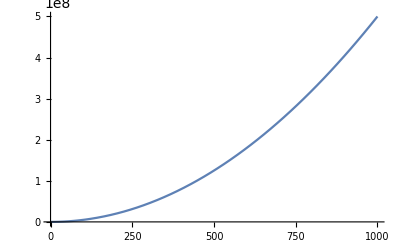

```mathematica
params={nT->10^5,μ->10^(-7),s->1.4};
Plot[(nT^2 μ (s t Log[(-1+ⅇ^(s t)+nT)/(-1+nT)]-PolyLog[2,1/(1-nT)]+PolyLog[2,-ⅇ^(s t)/(-1+nT)]))/s^2/.params,{t,0,1000}]
```

```mathematica
m1[t_,params_]:=nT μ t/.params
m2[t_,params_]:=(μ)^2 nT t (nT^2 μ (s t Log[(-1+ⅇ^(s t)+nT)/(-1+nT)]-PolyLog[2,1/(1-nT)]+PolyLog[2,-ⅇ^(s t)/(-1+nT)]))/s^2/.params
```

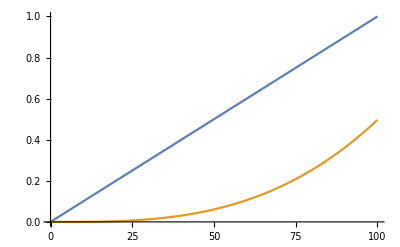

```mathematica
params={nT->10^5,μ->10^(-7),s->1.4};
Plot[{m1[t,params], m2[t,params]},{t,0,100}]
```